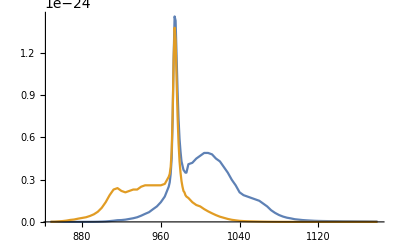

```mathematica
Clear["Global`*"]

(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;

ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All]

σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->1];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->1];
```

```mathematica
c=3 10^8;(*м/с*)
τ=1.45 10^-3;(*с*)
NN=300;(*ppm*)
NN=6.62 10^22 NN;(*1/м^3*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 7^2 10^-12;(*Эффективная площадь моды*)

Ps=Aeff h c/(λs 10^-9);
Pp=Aeff h c/(λp 10^-9);

L=2;
```

```mathematica
σa[λp]
```

```mathematica
(*Усилитель малого сигнала*)
soln2=Solve[0==ρp[z](σap (NN-N2[z])-σep N2[z]),N2[z]]
```

{{N2[z]→(1.986×10^25 σap ρp[z])/(σap ρp[z]+σep ρp[z])}}

```mathematica
{ρp'[z]==ρp[z](σep* N2[z]-σap* (NN-N2[z])), 
Pp ρp[0]==Pp0}/.soln2
```

{{ρp'[z]==ρp[z] ((1.986×10^25 σap σep ρp[z])/(σap ρp[z]+σep ρp[z])-σap (1.986×10^25-(1.986×10^25 σap ρp[z])/(σap ρp[z]+σep ρp[z]))),(7.65457×10^-27 ρp[0])/λp==Pp0}}

```mathematica
t1=Timing[sol=DSolve[{ρp'[z]==ρp[z](σep* N2[z]-σap* (NN-N2[z])), 
Pp ρp[0]==Pp0}/.soln2,ρp[z],z]][[1]]
```

0.002892

```mathematica
sol
```

{{ρp[z]→1.30641×10^26 Pp0 λp}}

{{N2[z]→(1.986×10^25 ρp[z] InterpolatingFunction[{{848., 1180.}}, <>][λp])/(689.655+ρp[z] InterpolatingFunction[{{848., 1180.}}, <>][λp]+ρp[z] InterpolatingFunction[{{848., 1180.}}, <>][λp])}}

```mathematica
Plot[Pp ρp[z]/.sol/.{Pp0->1,Ps0->1,λp->960,λs->1064},{z,0,L}]
```

DSolve::dsvar: 0.0000408571 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{0==-689.655 N2[0.0000408571]+ρp[0.0000408571] (Times[«3»]+Times[«2»]),«4»,(7.65457×10^-27 ρs[0])/λs==Ps0},{ρp,ρs,N1,N2},0.0000408571]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 0.0000408571 cannot be used as a variable.

ReplaceAll::reps: {DSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 0.0000408571 cannot be used as a variable.

General::stop: Further output of DSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {DSolve[{0.==-689.655 N2[0.0000408571]+(Times[«2»]+Times[«2»]) ρp[0.0000408571],«4»,7.19414×10^-30 ρs[0.]==1.},{ρp,ρs,N1,N2},0.0000408571]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-